# Closed-Form Approach to Oscillatory Integrals in Level-Crossing Physics

## Analytical Analysis

Maseim Bassis Kenmoe

University of Dschang

20.06.2025

## I. Derivative of the Modified Parabolic Cylinder Weber functions

### Derivative of Modified Parabolic Cylinder Weber functions

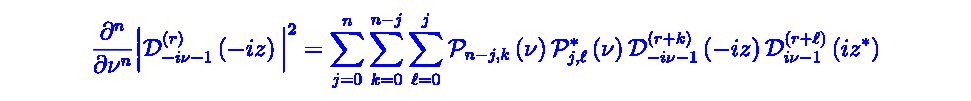
```mathematica
(*-Graphics-*)

DevModParabolicCylinderD[r_,n_,ν_]:=∑_(k=0)^n ∑_(m=0)^(n-k) ∑_(l=0)^k Binomial[n,k]P[n-k,m][ν]Q[k,l][ν]modAnaPCF[r+m,ν]modAnaPCFconj[r+l,ν];
```

### Polynomials

```mathematica
P[n_,m_][ν_]:=Which[n<m,0,m<0,0,n==m,(-ⅈ)^n,n≠m,Binomial[n,m](-ⅈ)^m (TnuPower[n-m-1,g1[nu]]/.{nu->ν})];

Q[n_,m_][ν_]:=Which[n<m,0,m<0,0,n==m,(ⅈ)^n,n≠m,Binomial[n,m](ⅈ)^m (TnuPowerConj[n-m-1,g2[nu]]/.{nu->ν})];
```

### Operator T

```mathematica
f[z_,p_,N1_]:=Exp[-z^2/4]/Gamma[-p]*Sum[(-z)^n/n!*2^((n-p-2)/2)*Gamma[(n-p)/2],{n,0,N1}];

g[z_,p_,N1_]:=Exp[-z^2/4]/Gamma[-p]*Sum[(-z)^n/n!*2^((n-p)/2)*Gamma[(n-p)/2]*PolyGamma[0,(n-p)/2],{n,0,N1}];

f1[nu_]:=PolyGamma[0,-(-ⅈ nu-1)]-Log[2]/2; f2[nu_]:=PolyGamma[0,-(ⅈ nu-1)]-Log[2]/2;

g1[nu_]:=-ⅈ f1[nu];  g2[nu_]:=ⅈ f2[nu];

T1[expr_]:=D[expr,nu]-ⅈ f1[nu]*expr; T2[expr_]:=D[expr,nu]+ⅈ f2[nu]*expr;

(*General function:T^n applied to g[nu]*)
TnuPower[n_Integer,expr_]:=Nest[T1,expr,n];

TnuPowerConj[n_Integer,expr_]:=Nest[T2,expr,n]
```

### Formatting

```mathematica
formatD[expr_]:=RowBox[{SubsuperscriptBox[StyleBox["D",FontSlant->"Plain"],RowBox[{"-","1"}],RowBox[{"(",ToBoxes[expr],")"}]]}]

formatDConj[expr_]:=RowBox[{SubsuperscriptBox[StyleBox["D",FontSlant->"Plain"],RowBox[{"-","1"}],RowBox[{"(",ToBoxes[expr],")","*"}]]}]
```

### List replacement

```mathematica
(*This list allows to express the modified Parabolic Cylinder Functions into Real and Imaginary parts*)

list1[val_]:=Flatten[Table[If[a≠b,{modAnaPCF[a+r,0] modAnaPCFconj[b+r,0]->re[modAnaPCF[a+r,0] modAnaPCFconj[b+r,0]]+I im[modAnaPCF[a+r,0] modAnaPCFconj[b+r,0]],modAnaPCF[b+r,0] modAnaPCFconj[a+r,0]->re[modAnaPCF[a+r,0] modAnaPCFconj[b+r,0]]-I im[modAnaPCF[a+r,0] modAnaPCFconj[b+r,0]]},Unevaluated[Sequence[]]],{a,0,val},{b,0,val}]];

(*This list allows to format the Modified PCF*)

list2[val_]:=Join[Table[modAnaPCF[a+r,0]->DisplayForm/@{formatD[r]},{a,0,val}],Table[modAnaPCFconj[a+r,0]->DisplayForm/@{formatDConj[r+a]},{a,0,val}]]
```

### Calculations

```mathematica
(* n is the Order of the derivative*)

DevOder[n_Integer]:=FullSimplify[Collect[Expand[FullSimplify[DevModParabolicCylinderD[r,n,0]]],modAnaPCF[r,0] modAnaPCFconj[r,0]]/.list1[n]]/.list2[n]
```

## II. Illustrative examples

### First Order

```mathematica
DevOder[1]
```

-2 im[{D_-1^(r) D_-1^((1+r)*)}]

### Second Order

```mathematica
DevOder[2]
```

{1/3 π^2 D_-1^(r) D_-1^((r)*)+2 D_-1^(r) D_-1^((1+r)*)-2 re[{D_-1^(r) D_-1^((2+r)*)}]}

### Third Order

```mathematica
DevOder[3]
```

-2 π^2 im[{D_-1^(r) D_-1^((1+r)*)}]-6 im[{D_-1^(r) D_-1^((2+r)*)}]+2 im[{D_-1^(r) D_-1^((3+r)*)}]

### Fourth Order

```mathematica
Expand[DevOder[4]]
```

{1/5 π^4 D_-1^(r) D_-1^((r)*)+4 π^2 D_-1^(r) D_-1^((1+r)*)+6 D_-1^(r) D_-1^((2+r)*)-4 π^2 re[{D_-1^(r) D_-1^((2+r)*)}]-8 re[{D_-1^(r) D_-1^((3+r)*)}]+2 re[{D_-1^(r) D_-1^((4+r)*)}]}

### Fifth Order

```mathematica
Expand[DevOder[5]]
```

-2 π^4 im[{D_-1^(r) D_-1^((1+r)*)}]-20 π^2 im[{D_-1^(r) D_-1^((2+r)*)}]-20 im[{D_-1^(r) D_-1^((3+r)*)}]+20/3 π^2 im[{D_-1^(r) D_-1^((3+r)*)}]+10 im[{D_-1^(r) D_-1^((4+r)*)}]-2 im[{D_-1^(r) D_-1^((5+r)*)}]